## Bose Hubbard Distributions and Scaling

### All of the following calculations are done at effective infinite temperature. So this is really independent of what the bose-hubbard hamiltonian is, just populates all possible basis states equally. This helps provide some intuition for what the long-time properties of the system are after a hard quench. Certainly in the case of trying to guess the “thermal” expectation.

#### # of states in subsystem A

```mathematica
ns[n_,L_]:=(((n+L/2-1)!)/(n!(L/2-1)!))
```

#### Normalized now by P(# of atoms in system size)

```mathematica
pn2[n_,L_]:=((((L-n)+L/2-1)!)/((L-n)!(L/2-1)!)) (((n+L/2-1)!)/(n!(L/2-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnln[n_,l_,L_]:=((((L-n)+l-1)!)/((L-n)!(l-1)!)) (((n+(L-l)-1)!)/(n!((L-l)-1)!))/(((L+L-1)!)/(L!(L-1)!))
```

#### Testing Distributions(normalization)

```mathematica
TestMENormalize=N[Table[Sum[pn2[n,L],{n,0,L}],{L,2,40}]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Testing Distribution shape
```

Distribution shape Testing

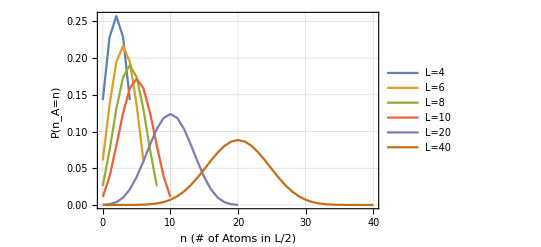

```mathematica
ListPlot[{Table[{n,pn2[n,4]},{n,0,4}],
Table[{n,pn2[n,6]},{n,0,6}],
Table[{n,pn2[n,8]},{n,0,8}],
Table[{n,pn2[n,10]},{n,0,10}],
Table[{n,pn2[n,20]},{n,0,20}],
Table[{n,pn2[n,40]},{n,0,40}]
},
PlotLegends-> {"L=4","L=6","L=8","L=10","L=20","L=40"},
Joined-> True,
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"n (# of Atoms in L/2)","P(n_A=n)","Bose Hubbard T=Infinity"}
]
```

```mathematica
(*Normalization Check*)
Sum[pn2[ii,6],{ii,0,6}]
```

1

```mathematica
(*Normalization Check*)
Sum[pnln[ii,4,8],{ii,0,8}]
```

1

## Calculating S_p from the P(n_A=n) when L_A=L/2

S_p is the von Neuman entropy in just the particle-number sector of the reduced density matrix.
This is discussed in the SI of https://arxiv.org/abs/1805.09819 

Generically, total entanglement entropy of a “thermalized” quantum state is expected to scale as a volume law (i.e. linearly with subsystem size since this is a 1D system)

However, we see below that if we consider just the particle number sector this is not the case but something more like an area law + log correction, or just a log(L) scaling.

```mathematica
sp[L_]:=-Sum[pn2[n,L]Log[pn2[n,L]]
,
{n,0,L}
]
```

```mathematica
Scaling of Sp for system size L and sub system always L/2 (linear plot)
```

1/2 always and for L^2 linear of plot Scaling size Sp sub system^2

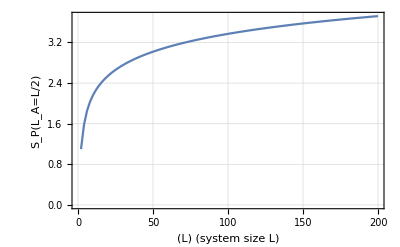

```mathematica
spvals=Table[{l,sp[l]},{l,2,200,2}];
ListPlot[{spvals},
Joined-> True,
Frame-> True,
FrameLabel-> {"(L) (system size L)","S_P(L_A=L/2)","Scaling of S_P"},
GridLines-> Automatic
]
```

```mathematica
Scaling of Sp for system size L and sub system always L/2 (log plot)
```

1/2 always and for L^2 log of plot Scaling size Sp sub system^2

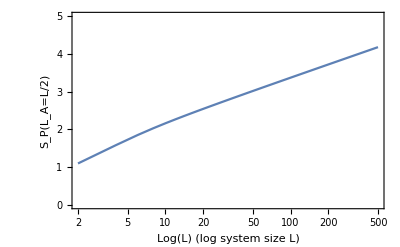

```mathematica
spvals=Table[{l,sp[l]},{l,2,500,2}];
ListLogLinearPlot[{spvals},
PlotRange->{ {2,500},{0,5}},
Joined-> True,
Frame-> True,
FrameLabel-> {"Log(L) (log system size L)","S_P(L_A=L/2)","Scaling of S_P"},
GridLines-> Automatic
]
```

## What about Fluctuations?

So this is a comparison now to the number fluctuations in a subsystem of size l=L/2 instead of number entropy

Interestingly, we see that this metric in fact does linearly growth with the subsystem size in this thermalized regime.

```mathematica
nf2[L_]:=Sum[pn2[n,L] n^2,{n,0,L}]-Sum[pn2[n,L]n,{n,0,L}]^2
```

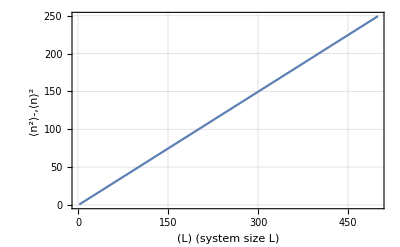

```mathematica
nfvals=Table[{l,nf2[l]},{l,2,500,2}];
ListPlot[{nfvals},
Joined-> True,
Frame-> True,
FrameLabel-> {"(L) (system size L)","⟨n^2⟩-,⟨n⟩^2","Scaling of Fluctuations"},
GridLines-> Automatic
]
```

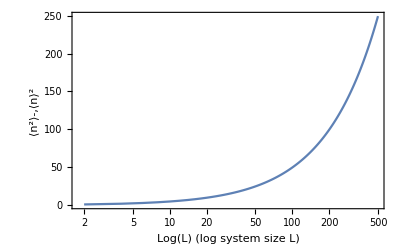

```mathematica
nfvals=Table[{l,nf2[l]},{l,2,500,2}];
ListLogLinearPlot[{nfvals},
Joined-> True,
Frame-> True,
FrameLabel-> {"Log(L) (log system size L)","⟨n^2⟩-,⟨n⟩^2","Scaling of Fluctuations"},
GridLines-> Automatic
]
```

#### Just to get some feeling for the distributions at infinite temperature

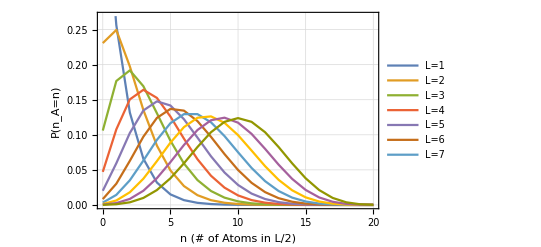

```mathematica
pnln[n_,l_,L_]:=((((L-n)+(L-l)-1)!)/((L-n)!((L-l)-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((L+L-1)!)/(L!(L-1)!))

ListPlot[{Table[{n,pnln[n,1,20]},{n,0,20}],
Table[{n,pnln[n,2,20]},{n,0,20}],
Table[{n,pnln[n,3,20]},{n,0,20}],
Table[{n,pnln[n,4,20]},{n,0,20}],
Table[{n,pnln[n,5,20]},{n,0,20}],
Table[{n,pnln[n,6,20]},{n,0,20}],
Table[{n,pnln[n,7,20]},{n,0,20}],
Table[{n,pnln[n,8,20]},{n,0,20}],
Table[{n,pnln[n,9,20]},{n,0,20}],
Table[{n,pnln[n,10,20]},{n,0,20}]
},
PlotLegends-> {"L=1","L=2","L=3","L=4","L=5","L=6","L=7"},
Joined-> True,
Frame-> True,
GridLines-> Automatic,
FrameLabel-> {"n (# of Atoms in L/2)","P(n_A=n)","Bose Hubbard T=∞"}
]
```

#### One question now becomes how do these fluctuations of subsystem scaling compare at small subsystem size for larger and larger system sizes. We see here that they approach a volume law (or look linear) asymptotically for large systems

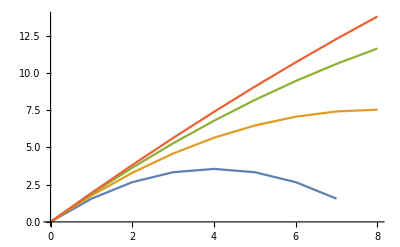

```mathematica
pn2[n_,L_]:=((((L-n)+L/2-1)!)/((L-n)!(L/2-1)!)) (((n+L/2-1)!)/(n!(L/2-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnln[n_,l_,L_]:=((((L-n)+(L-l-1))!)/((L-n)!(L-l-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((L+L-1)!)/(L!(L-1)!))
pnF[l_,L_]:=Total[Table[pnln[n,l,L] n^2,{n,1,L}]]-Total[Table[pnln[n,l,L]n,{n,1,L}]]^2
ListPlot[{Table[{l,pnF[l,8]},{l,0,7}],
Table[{l,pnF[l,16]},{l,0,8}],
Table[{l,pnF[l,32]},{l,0,8}],
Table[{l,pnF[l,64]},{l,0,8}]},
Joined-> True]
```

```mathematica
FullSimplify[pnF[l,L]/L];
```

Table::iterb: Iterator {n,1,L} does not have appropriate bounds.

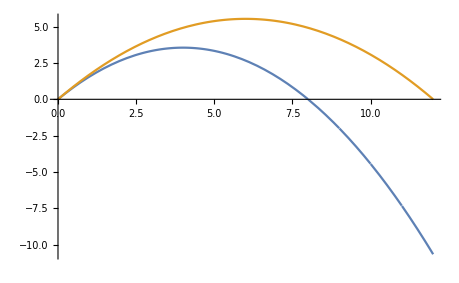

```mathematica
Plot[{pnF[l,8],pnF[l,12]},{l,0,12}]
```

## Fluctuations Formula in General

This section now generalizes how the fluctuations scale as a function of subsystem size and given filling (number of atoms:: Nt, in total system size of L)

```mathematica
pnlnN[n_,Nt_,l_,L_]:=((((Nt-n)+(L-l)-1)!)/((Nt-n)!((L-l)-1)!)) (((n+(l)-1)!)/(n!((l)-1)!))/(((Nt+L-1)!)/(Nt!(L-1)!))
pnFN[l_,L_,NE_]:=Sum[pnlnN[n,NE,l,L] n^2,{n,0,NE}]-Sum[pnlnN[n,NE,l,L]n,{n,0,NE}]^2
FullSimplify[pnFN[l,L,n]] (*this, even simplified, is not particularly englightening from here*)
```

Let’s look at a few test cases to find the general formulation
pnFN includes the fluctuations across all possible “n” values in subsystem size “l”. So all we really want are the fluctuation in a system of fixed particle number NE, size L, and at given subsystem of size “l”

```mathematica
FullSimplify[pnFN[l,L,1]]
FullSimplify[pnFN[l,L,2]]
FullSimplify[pnFN[l,L,3]]
FullSimplify[pnFN[l,L,4]]
FullSimplify[pnFN[l,L,5]]
FullSimplify[pnFN[l,L,10]]
```

(l (-l+L))/L^2

(2 l (2+L) (-l+L))/(L^2 (1+L))

-(3 l (l-L) (3+L))/(L^2 (1+L))

-(4 l (l-L) (4+L))/(L^2 (1+L))

-(5 l (l-L) (5+L))/(L^2 (1+L))

-(10 l (l-L) (10+L))/(L^2 (1+L))

So from the above examples we can figure out the generic formulation is as shown below

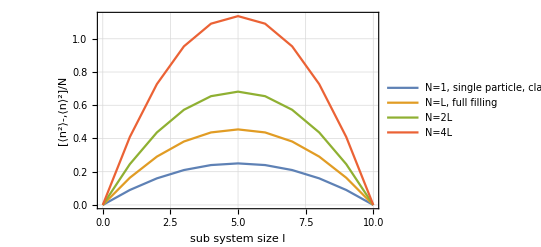

```mathematica
pnFG[l_,L_,n_]:=(n l(L-l)(L+n))/(L^2(L+1))
pnFGNorm[l_,L_,n_]:=(l(L-l)(L+n))/(L^2(L+1)) (*we could normalize by the number of particles involved, there is a reason to do this explained later*)
ListPlot[{Table[{l,pnFGNorm[l,10,1]},{l,0,10}],
Table[{l,pnFGNorm[l,10,10]},{l,0,10}],
Table[{l,pnFGNorm[l,10,20]},{l,0,10}],
Table[{l,pnFGNorm[l,10,40]},{l,0,10}]},
Frame-> True,
FrameLabel-> {"sub system size l","[⟨n^2⟩-,⟨n⟩^2]/N","Scaling of Fluctuations per particle"},
PlotLegends-> {"N=1, single particle, classical case","N=L, full filling","N=2L","N=4L"},
GridLines-> Automatic,
Joined-> True
]
```

So the interesting note to be taken away from this plot is that regardless of the filling or system size, the particle number fluctuations always follow that of a parabola for the total system size. This makes sense intuitively since in the single-particle regime we can faithfully think of this system as a coin-flip problem where the x-axis becomes a scale of probability of fairness of the coin that is decided by l/L. In this system this probability is purely the likelihood of finding a particle in subsystem of size l given total size L. Then the variance of the sampled coin flips (or single-particle number) would become the number fluctuations we measure here. The reason we normalize by total particle number is because in the classical case this plot would remain the same regardless of how many coins we are flipping. However, in this case we have bosonic enhancement that will being to play a larger and larger role as we shove more bosons into the syste. Hence the scaling of the curves up as we pack in more particles.

## Hilbert Space Size

Just for comparison of how the hilbert space size grows compared to what the fluctuations reveal from scaling of a subsystem.
to be expanded later

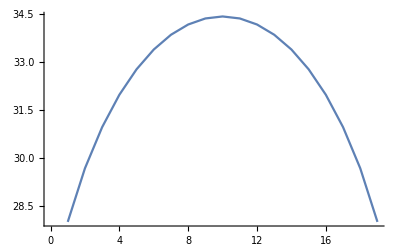

```mathematica
NL[n_,l_,L_]:=((((L-n)+l-1)!)/((L-n)!(l-1)!)) 
NR[n_,l_,L_]:=(((n+(L-l)-1)!)/(n!((L-l)-1)!))
NLR[l_,NT_]:=Sum[NL[ii,l,NT],{ii,0,NT}] Sum[NR[ii,l,NT],{ii,0,NT}];

NLP=20;
ListPlot[
{
Table[{l, Log[NLR[l,NLP]]},{l,1,NLP-1}]
},
Joined-> True
]
```